```mathematica
denominator[x_]:=If[x==0, 1, Abs[x]^(2/3)+Sign[x] Abs[x]^(1/3)+1]
```

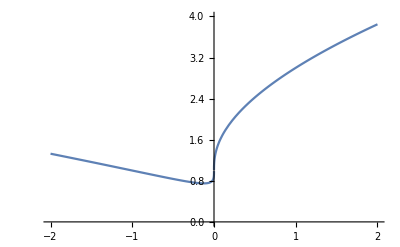

```mathematica
Plot[denominator[x], {x, -2, 2}, PlotRange->{{-2, 2},{0, 4}}, PlotPoints->100, MaxRecursion->15]
```

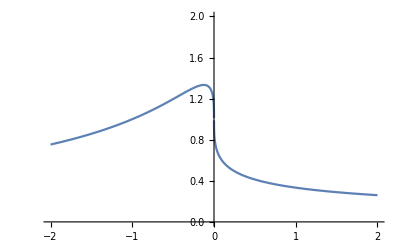

```mathematica
Plot[1/denominator[x], {x, -2, 2}, PlotRange->{{-2, 2},{0, 2}}, PlotPoints->100, MaxRecursion->15]
```